CSE 577 * Dianne Hansford
Homework 1: Font Design
Due February 16, 2016 by midnight

### Turn in via Blackboard Name your file srivastava_anant_HW1.nb

Using several cubic Bezier curves, design two characters, for instance your two initials. These can be Western, Chinese, Sanskrit, Arabic, etc., fonts.
The characters need to have a thickness, or in other words, an inside. See the class log for a link to some examples from a previous semester. Be creative!
(You do not need to fill-in the characters.)

Produce the following plots.
1) Bezier polygons, control points, and curves. Use different colors and line thickness to make the plot interesting.
2) Just the curves
3) Apply a shear matrix to make italic versions of your characters.
4) A Manipulate environment with a point that moves around the outside curves of one of the characters.

For part 4, use your own implemention of the de Casteljau algorithm. (See chapter 4, slide 9) This part will also require you to write a global to local parameter transformation routine.

Please put the functions/subroutines at the beginning of the notebook for easy grading.
Comments are required and will count toward your grade.

```mathematica
1. All plots, polygons curves, control points. characters: a, s.
```

{{0,200},{400,-200},{0,220},{400,-180},{220,20},{150,-200},{220,0},{150,-180},{140,-80},{130,-130}}

{{140,180},{120,125},{120,115},{80,60},{140,200},{80,50}}

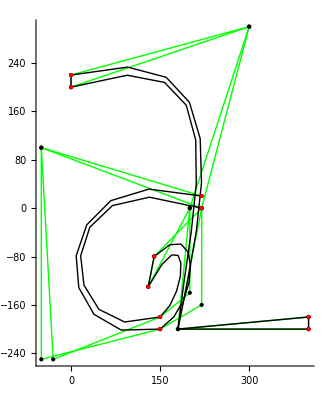

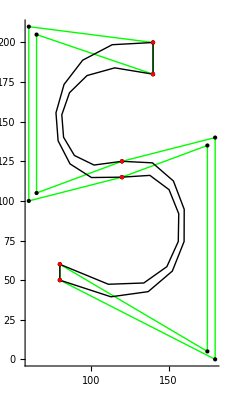

```mathematica
(*dca is used to calculate the points in the Bezier Curve, so that the 
curvy part can be integrated into a polygon to be colored. 
Those points are also used to create lines to color the curvy surfaces*)

SetAttributes[dcai,HoldAll]
dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];

(* Iterative de-casteljau's algorithm for plotting a dynamic point (part 4)*)

dcai[b_,r_,i_,t_]:=Module[{bb=b},For[k=1,k≤r,k++,For[j=i,j≤r-k,j++,bb[[j+1]]=(1-t)*bb[[j+1]]+t*bb[[j+2]];]];bb[[i+1]]]

(* Function to create a nested traversal for all the curves constituting 's' uses iterative dca *)

curvept[t_]:=If[t ≤ 1 ,Graphics[{PointSize[Large],Red,Point[dca[ba1,n1,0,t]]}],
If[t≤2,Graphics[{PointSize[Large],Red,Point[dcai[ba2,n2,0,t-1]]}],
If[t≤3,Graphics[{PointSize[Large],Red,Point[dcai[ba4,n4,0,t-2]]}],
If[t≤4,Graphics[{PointSize[Large],Red,Point[dcai[ba3,n3,0,t-3]]}],
If[t≤5, Graphics[{PointSize[Large],Red,Point[dcai[ba5,n5,0,t-4]]}],
Graphics[{PointSize[Large],Red,Point[dcai[ba6,1,0,t-5]]}]
]
]
]
]
];



(*Control points for a*)

bb1 = {{0, 200}, {300, 300}, {200, 0}, {180, -200}, {400, -200}}; 
bb2 = {{0, 220}, {300, 300}, {220, 0}, {180, -200}, {400, -180}};
bb3 = {{400,-180},{400,-200}};
bb4 = {{0,200},{0,220}};
bb5 = {{220,20},{-50,100},{-50,-250},{150,-200}};
bb6 = {{220,0},{-50,100},{-30,-250},{150,-180}};
bb7 = {{150,-200},{220,-160},{220,0},{140,-80}};
bb8 = {{150,-180},{200,-140},{200,0},{130,-130}};
bb9 = {{140,-80},{130,-130}};

(* Testing affine Transformaations *)
shear = {{1,0},{0,1}};
b1 = bb1.shear; 
b2 = bb2.shear;
b3 = bb3.shear;
b4 = bb4.shear;
b5 = bb5.shear;
b6 = bb6.shear;
b7=  bb7.shear;
b8 = bb8.shear;
b9 = bb9.shear;


(*Degrees*)
n1 = Length[b1] - 1; 
n2 = Length[b2] - 1;
n3 = Length[b3] - 1;
n4 = Length[b4] - 1;
n5 = Length[b5] - 1;
n6 = Length[b6] - 1;
n7 = Length[b7] - 1;
n8 = Length[b8] - 1;
n9 = Length[b9] - 1;


(*Curves*)
curve1 = Graphics[{Thick, BezierCurve[b1,SplineDegree->n1]}];
curve2 = Graphics[{Thick, BezierCurve[b2,SplineDegree->n2]}];
curve3 = Graphics[{Thick, Line[b3]}];
curve4 = Graphics[{Thick, Line[b4]}];
curve5 = Graphics[{Thick, BezierCurve[b5,SplineDegree->n5]}];
curve6 = Graphics[{Thick, BezierCurve[b6,SplineDegree->n6]}];
curve7 = Graphics[{Thick, BezierCurve[b7,SplineDegree->n7]}];
curve8 = Graphics[{Thick, BezierCurve[b8,SplineDegree->n8]}];
curve9 = Graphics[{Thick, Line[b9]}];

(*Control Ploygon Edges*)
poly1 = Graphics[{Green, Line[b1]}];
poly2 = Graphics[{Green, Line[b2]}];
poly3 = Graphics[{Green, Line[b3]}];
poly4 = Graphics[{Green, Line[b4]}];
poly5 = Graphics[{Green, Line[b5]}];
poly6 = Graphics[{Green, Line[b6]}];
poly7 = Graphics[{Green, Line[b7]}];
poly8 = Graphics[{Green, Line[b8]}];
poly9 = Graphics[{Green, Line[b9]}];

(*Control Points*)
points1 = Graphics[{PointSize[Medium], Point[b1]}];
points2 = Graphics[{PointSize[Medium], Point[b2]}];
points3 = Graphics[{PointSize[Medium], Point[b3]}];
points4 = Graphics[{PointSize[Medium], Point[b4]}];
points5 = Graphics[{PointSize[Medium], Point[b5]}];
points6 = Graphics[{PointSize[Medium], Point[b6]}];
points7 = Graphics[{PointSize[Medium], Point[b7]}];
points8 = Graphics[{PointSize[Medium], Point[b8]}];
points9 = Graphics[{PointSize[Medium], Point[b9]}];

(*Lines calculated using dca*)
line11=Line[Table[dca[b1,n1,0,t],{t,0,1,0.01}]];
line12=Line[Table[dca[b2,n2,0,t],{t,0,1,0.01}]];
line13=Line[Table[dca[b3,n3,0,t],{t,0,1,0.05}]];
line14=Line[Table[dca[b4,n4,0,t],{t,0,1,0.05}]];
line15=Line[Table[dca[b5,n5,0,t],{t,0,1,0.05}]];
line16=Line[Table[dca[b6,n6,0,t],{t,0,1,0.05}]];
line17=Line[Table[dca[b7,n7,0,t],{t,0,1,0.05}]];
line18=Line[Table[dca[b8,n8,0,t],{t,0,1,0.05}]];
line19 = Line[b9];

(*control points for s *)
ba1 = {{140,180},{65,205},{65,105},{120,125}}.shear;
ba2 = {{120,125},{180,140},{180,0},{80,50}}.shear;
ba3 = {{80,60},{175,5}, {175,135},{120, 115}}.shear;
ba4 = {{80,50},{80,60}}.shear;
ba5 = {{120,115},{60,100},{60,210},{140,200}}.shear;
ba6 = {{140,200},{140,180}}.shear;

(*Degrees*)
n1 = Length[ba1] - 1; 
n2 = Length[ba2] -1;
n3 = Length[ba3] -1;
n4 = Length[ba4] -1;
n5 = 3;

(*Curves*)
curve21 = Graphics[{Thick, BezierCurve[ba1,SplineDegree->n1]}];
curve22 = Graphics[{Thick, BezierCurve[ba2,SplineDegree->n2]}];
curve23 = Graphics[{Thick, BezierCurve[ba3,SplineDegree->n3]}];
curve24 = Graphics[{Thick, Line[ba4]}];
curve25 = Graphics[{Thick, BezierCurve[ba5,SplineDegree->n5]}];
curve26 = Graphics[{Thick, Line[ba6]}];

(*Control Ploygon Edges*)
poly21 = Graphics[{Green, Line[ba1]}];
poly22 = Graphics[{Green, Line[ba2]}];
poly23 = Graphics[{Green, Line[ba3]}];
poly24 = Graphics[{Green, Line[ba4]}];
poly25 = Graphics[{Green, Line[ba5]}];
poly26 = Graphics[{Green, Line[ba6]}];

(*Control Points*)
points21 = Graphics[{PointSize[Medium], Point[ba1]}];
points22 = Graphics[{PointSize[Medium], Point[ba2]}];
points23 = Graphics[{PointSize[Medium], Point[ba3]}];
points24 = Graphics[{PointSize[Medium], Point[ba4]}];
points25 = Graphics[{PointSize[Medium], Point[ba5]}];
points26 = Graphics[{PointSize[Medium], Point[ba6]}];

(*Lines calculated using dca*)
line21=Line[Table[dca[ba1,n1,0,t],{t,0,1,0.01}]];
line22=Line[Table[dca[ba2,n2,0,t],{t,0,1,0.01}]];
line23=Line[Table[dca[ba3,n3,0,t],{t,0,1,0.05}]];
line24=Line[Table[dca[ba4,1,0,t],{t,0,1,0.05}]];
line25=Line[Table[dca[ba5,n5,0,t],{t,0,1,0.05}]];
line26=Line[Table[dca[ba6,1,0,t],{t,0,1,0.05}]];

(*Outline of the curves*)
graphs1 = Graphics[{Thick, line11,line12,line13,line14,line15,line16,line17,line18,line19}];
graphs2 = Graphics[{Thick, line21,line22,line23,line24,line25,line26}];

(*end points are set red other points are balck and medium *)
end1 = {{0,200},{400,-200},{0,220},{400,-180},{220,20},{150,-200},{220,0},{150,-180},{140,-80},{130,-130}}.shear
endpts1 = Graphics[{PointSize[Large], Red, Point[end1]}];

(*end points are set red other points are balck and medium *)
end2 = {{140,180},{120,125},{120, 115},{80,60},{140,200},{80,50}}.shear
endpts2 = Graphics[{PointSize[Large], Red, Point[end2]}];

(*Show the plot with control points*)
Show[{
poly1, poly2, poly3, poly4, poly5, poly6, poly7, poly8, poly9, 
curve1, curve2, curve3, curve4, curve5, curve6,curve7,curve8, curve9, 
points1, points2, points3, points4, points5, points6, points7, points8, points9,
endpts1
}, Axes -> True]

Show[{
poly21,poly22,poly23,poly24,poly25,poly26,
curve21,curve22,curve23,curve24,curve25,curve26,
points21,points22,points23,points24,points25,points26,
endpts2
}, Axes -> True]
```

```mathematica
2.)Just the curves.
```

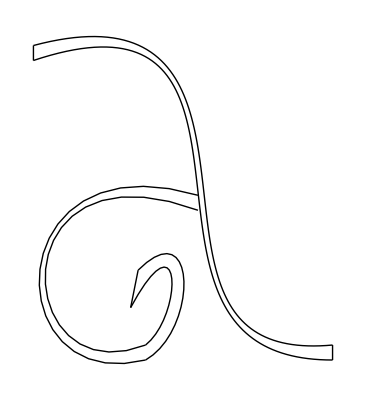

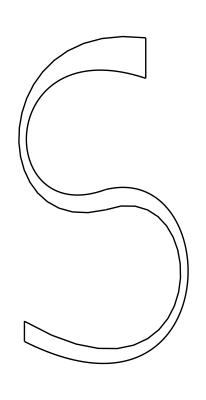

```mathematica
(* Show the graph with curves *)
Show[{graphs1}, Axes -> False]
Show[{graphs2}, Axes -> False]
```

### 3.) Using Shear matrix to italicize.

{{200,400},{200,-400},{220,440},{220,-360},{240,40},{-50,-400},{220,0},{-30,-360},{60,-160},{0,-260}}

{{320,360},{245,250},{235,230},{140,120},{340,400},{130,100}}

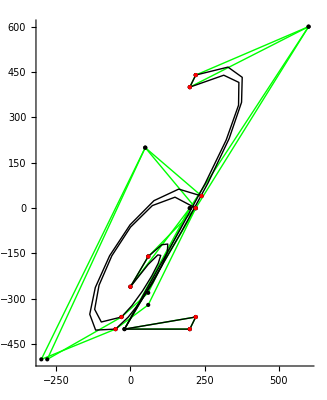

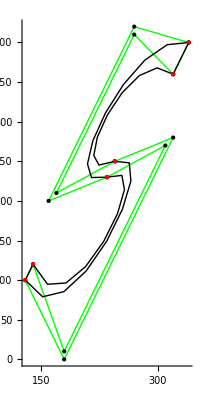

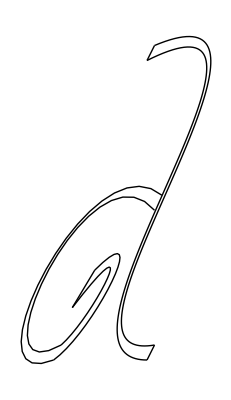

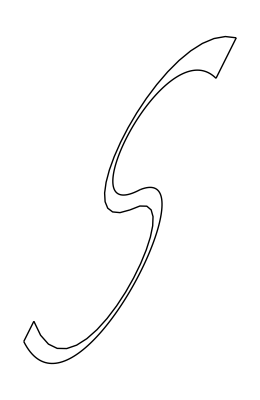

```mathematica
(*dca is used to calculate the points in the Bezier Curve, so that the 
curvy part can be integrated into a polygon to be colored. 
Those points are also used to create lines to color the curvy surfaces*)

dca[b_,r_,i_,t_]:=If [r==0,b[[i+1]],(1-t)*dca[b,r-1,i,t]+t*dca[b,r-1,i+1,t]];
bb1 = {{0, 200}, {300, 300}, {200, 0}, {180, -200}, {400, -200}}; 
bb2 = {{0, 220}, {300, 300}, {220, 0}, {180, -200}, {400, -180}};
bb3 = {{400,-180},{400,-200}};
bb4 = {{0,200},{0,220}};
bb5 = {{220,20},{-50,100},{-50,-250},{150,-200}};
bb6 = {{220,0},{-50,100},{-30,-250},{150,-180}};
bb7 = {{150,-200},{220,-160},{220,0},{140,-80}};
bb8 = {{150,-180},{200,-140},{200,0},{130,-130}};
bb9 = {{140,-80},{130,-130}};

(*
using shear matrix italacize a and s 
The rest of the code is the same as above
*)
shear = {{1,0},{1,2}};
b1 = bb1.shear; 
b2 = bb2.shear;
b3 = bb3.shear;
b4 = bb4.shear;
b5 = bb5.shear;
b6 = bb6.shear;
b7=  bb7.shear;
b8 = bb8.shear;
b9 = bb9.shear;
n1 = Length[b1] - 1; 
n2 = Length[b2] - 1;
n3 = Length[b3] - 1;
n4 = Length[b4] - 1;
n5 = Length[b5] - 1;
n6 = Length[b6] - 1;
n7 = Length[b7] - 1;
n8 = Length[b8] - 1;
curve1 = Graphics[{Thick, BezierCurve[b1,SplineDegree->n1]}];
curve2 = Graphics[{Thick, BezierCurve[b2,SplineDegree->n2]}];
curve3 = Graphics[{Thick, Line[b3]}];
curve4 = Graphics[{Thick, Line[b4]}];
curve5 = Graphics[{Thick, BezierCurve[b5,SplineDegree->n5]}];
curve6 = Graphics[{Thick, BezierCurve[b6,SplineDegree->n6]}];
curve7 = Graphics[{Thick, BezierCurve[b7,SplineDegree->n7]}];
curve8 = Graphics[{Thick, BezierCurve[b8,SplineDegree->n8]}];
curve9 = Graphics[{Thick, Line[b9]}];
poly1 = Graphics[{Green, Line[b1]}];
poly2 = Graphics[{Green, Line[b2]}];
poly3 = Graphics[{Green, Line[b3]}];
poly4 = Graphics[{Green, Line[b4]}];
poly5 = Graphics[{Green, Line[b5]}];
poly6 = Graphics[{Green, Line[b6]}];
poly7 = Graphics[{Green, Line[b7]}];
poly8 = Graphics[{Green, Line[b8]}];
poly9 = Graphics[{Green, Line[b9]}];
points1 = Graphics[{PointSize[Medium], Point[b1]}];
points2 = Graphics[{PointSize[Medium], Point[b2]}];
points3 = Graphics[{PointSize[Medium], Point[b3]}];
points4 = Graphics[{PointSize[Medium], Point[b4]}];
points5 = Graphics[{PointSize[Medium], Point[b5]}];
points6 = Graphics[{PointSize[Medium], Point[b6]}];
points7 = Graphics[{PointSize[Medium], Point[b7]}];
points8 = Graphics[{PointSize[Medium], Point[b8]}];
points9 = Graphics[{PointSize[Medium], Point[b9]}];
line11=Line[Table[dca[b1,n1,0,t],{t,0,1,0.01}]];
line12=Line[Table[dca[b2,n2,0,t],{t,0,1,0.01}]];
line13=Line[Table[dca[b3,n3,0,t],{t,0,1,0.05}]];
line14=Line[Table[dca[b4,n4,0,t],{t,0,1,0.05}]];
line15=Line[Table[dca[b5,n5,0,t],{t,0,1,0.05}]];
line16=Line[Table[dca[b6,n6,0,t],{t,0,1,0.05}]];
line17=Line[Table[dca[b7,n7,0,t],{t,0,1,0.05}]];
line18=Line[Table[dca[b8,n8,0,t],{t,0,1,0.05}]];
line19 = Line[b9];
ba1 = {{140,180},{65,205},{65,105},{120,125}}.shear;
ba2 = {{120,125},{180,140},{180,0},{80,50}}.shear;
ba3 = {{80,60},{175,5}, {175,135},{120, 115}}.shear;
ba4 = {{80,50},{80,60}}.shear;
ba5 = {{120,115},{60,100},{60,210},{140,200}}.shear;
ba6 = {{140,200},{140,180}}.shear;
n1 = Length[ba1] - 1; 
n2 = Length[ba2] -1;
n3 = Length[ba3] -1;
n4 = Length[ba4] -1;
n5 = 3;
curve21 = Graphics[{Thick, BezierCurve[ba1,SplineDegree->n1]}];
curve22 = Graphics[{Thick, BezierCurve[ba2,SplineDegree->n2]}];
curve23 = Graphics[{Thick, BezierCurve[ba3,SplineDegree->n3]}];
curve24 = Graphics[{Thick, Line[ba4]}];
curve25 = Graphics[{Thick, BezierCurve[ba5,SplineDegree->n5]}];
curve26 = Graphics[{Thick, Line[ba6]}];
poly21 = Graphics[{Green, Line[ba1]}];
poly22 = Graphics[{Green, Line[ba2]}];
poly23 = Graphics[{Green, Line[ba3]}];
poly24 = Graphics[{Green, Line[ba4]}];
poly25 = Graphics[{Green, Line[ba5]}];
poly26 = Graphics[{Green, Line[ba6]}];
points21 = Graphics[{PointSize[Medium], Point[ba1]}];
points22 = Graphics[{PointSize[Medium], Point[ba2]}];
points23 = Graphics[{PointSize[Medium], Point[ba3]}];
points24 = Graphics[{PointSize[Medium], Point[ba4]}];
points25 = Graphics[{PointSize[Medium], Point[ba5]}];
points26 = Graphics[{PointSize[Medium], Point[ba6]}];
line21=Line[Table[dca[ba1,n1,0,t],{t,0,1,0.01}]];
line22=Line[Table[dca[ba2,n2,0,t],{t,0,1,0.01}]];
line23=Line[Table[dca[ba3,n3,0,t],{t,0,1,0.05}]];
line24=Line[Table[dca[ba4,1,0,t],{t,0,1,0.05}]];
line25=Line[Table[dca[ba5,n5,0,t],{t,0,1,0.05}]];
line26=Line[Table[dca[ba6,1,0,t],{t,0,1,0.05}]];

graphs1 = Graphics[{Thick, line11,line12,line13,line14,line15,line16,line17,line18,line19}];
graphs2 = Graphics[{Thick, line21,line22,line23,line24,line25,line26}];
end1 = {{0,200},{400,-200},{0,220},{400,-180},{220,20},{150,-200},{220,0},{150,-180},{140,-80},{130,-130}}.shear
endpts1 = Graphics[{PointSize[Large], Red, Point[end1]}];

end2 = {{140,180},{120,125},{120, 115},{80,60},{140,200},{80,50}}.shear
endpts2 = Graphics[{PointSize[Large], Red, Point[end2]}];
Show[{
poly1, poly2, poly3, poly4, poly5, poly6, poly7, poly8, poly9, 
curve1, curve2, curve3, curve4, curve5, curve6,curve7,curve8, curve9, 
points1, points2, points3, points4, points5, points6, points7, points8, points9,
endpts1
}, Axes -> True]

Show[{
poly21,poly22,poly23,poly24,poly25,poly26,
curve21,curve22,curve23,curve24,curve25,curve26,
points21,points22,points23,points24,points25,points26,
endpts2
}, Axes -> True]
Show[{graphs1}, Axes -> False]
Show[{graphs2}, Axes -> False]
```

### 4.) Using de casteljau’s algorithm plot a point that moves on the outside of the alphabet.

```mathematica
(* the red point traces the outer of the shape f the alphabet 's'*)
(* this section uses the iterative version of de casteljau's algorithm*)

Manipulate[
Show[{points21,poly21,curve21,points22,poly22,curve22,
points23,poly23,curve23,points24,poly24,curve24,
points25,poly25,curve25,points26,poly26,curve26,
curvept[t]}, Boxed->False],
{t,0,6}]
Print["Trace of the curve's outer"];
```

Trace of the curve's outer